```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BTC Price | log return future | log return bitcoin
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 40143.7 | 0.0212907 | 0.018658
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 39401.7 | -0.0904653 | -0.0934764
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 43262.4 | -0.0196938 | -0.0216123
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 44207.6 | -0.131645 | -0.126287
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 50158.3 | 0.03685 | 0.0328265
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 48538.5 | -0.119603 | -0.11567
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 54490.5 | -0.042369 | -0.0388241
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 56647.7 | 0.018947 | 0.0163419
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 55729.5 | -0.0359909 | -0.0331504)

```mathematica
StringSplit[data[[2,2]]][[1]]
```

2021-05-20

```mathematica
data[[1,7]]
```

log return bitcoin

```mathematica
data[[1,6]]
```

log return future

```mathematica
α0=0.5; β0=0;
```

```mathematica
For[kk=29, kk≥1, kk--,
Print[kk];
SeedRandom[123456];
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
Print["Calibration..."];
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,6;;7⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

29

Calibration...

28

Calibration...

27

Calibration...

26

Calibration...

25

Calibration...

24

Calibration...

23

Calibration...

22

Calibration...

21

Calibration...

20

Calibration...

19

Calibration...

18

Calibration...

17

Calibration...

16

Calibration...

15

Calibration...

14

Calibration...

13

Calibration...

12

Calibration...

11

Calibration...

10

Calibration...

9

Calibration...

8

Calibration...

7

Calibration...

6

Calibration...

5

Calibration...

4

Calibration...

3

Calibration...

2

Calibration...

1

Calibration...

```mathematica
{α0,β0}
```

{0.898279,0.0437358}

```mathematica
For[kk=0, kk≤74, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{data⟦k,2⟧,{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,5⟧;
rbrr=data⟦2;;All,6⟧;
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,5⟧;
rf=data2⟦2;;All,6⟧;
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

1

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

2

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

3

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.982732907728307}. NIntegrate obtained 0.0644203 and 0.000177278 for the integral and error estimates.

4

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.979888994160487}. NIntegrate obtained 0.0651638 and 0.000105756 for the integral and error estimates.

5

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.982732907728307}. NIntegrate obtained 0.0659938 and 0.000113539 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

6

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

7

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

8

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

9

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

10

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

11

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

12

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

13

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

14

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

15

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

16

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

17

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

18

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

19

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

20

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

21

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

22

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

23

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

24

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

25

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

26

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

27

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

28

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

29

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

30

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

31

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

32

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

33

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

34

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

35

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

36

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

37

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

38

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

39

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

40

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

41

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

42

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

43

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

44

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

45

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

46

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

47

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

48

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

49

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

50

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

51

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

52

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

53

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

54

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

55

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

56

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

57

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

58

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

59

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

60

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

61

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

62

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

63

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

64

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

65

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

66

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

67

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

68

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

69

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

70

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

71

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

72

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

73

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

74

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-01-27 | 0.849951 | 0.694992 | 0.627041 | 0.597471 | 0.607707 | 0.649152
 | 2021-01-20 | 0.854168 | 0.70666 | 0.66224 | 0.605133 | 0.611839 | 0.664042
 | 2021-01-12 | 0.856987 | 0.716785 | 0.692939 | 0.604446 | 0.619633 | 0.677842
 | 2021-01-05 | 0.845162 | 0.705387 | 0.667221 | 0.608369 | 0.585342 | 0.66473
 | 2020-12-28 | 0.851118 | 0.705704 | 0.689765 | 0.598129 | 0.598996 | 0.679892
 | 2020-12-18 | 0.863627 | 0.725895 | 0.707762 | 0.625213 | 0.623383 | 0.687391
 | 2020-12-11 | 0.858774 | 0.723641 | 0.734744 | 0.602761 | 0.624204 | 0.696655
 | 2020-12-04 | 0.85316 | 0.719355 | 0.696875 | 0.613676 | 0.612866 | 0.674364
 | 2020-11-27 | 0.836567 | 0.706015 | 0.673248 | 0.600535 | 0.609957 | 0.628641
 | 2020-11-19 | 0.82448 | 0.693725 | 0.703651 | 0.569619 | 0.59387 | 0.641732
 | 2020-11-12 | 0.825645 | 0.704577 | 0.67623 | 0.591811 | 0.59511 | 0.625161
 | 2020-11-05 | 0.827582 | 0.690501 | 0.690669 | 0.575073 | 0.591699 | 0.63707
 | 2020-10-29 | 0.824865 | 0.688382 | 0.69068 | 0.57004 | 0.589632 | 0.640476
 | 2020-10-22 | 0.818579 | 0.684711 | 0.648974 | 0.578034 | 0.576749 | 0.608538
 | 2020-10-15 | 0.82012 | 0.67811 | 0.70158 | 0.560086 | 0.585077 | 0.620033
 | 2020-10-08 | 0.814322 | 0.671887 | 0.650773 | 0.570841 | 0.567441 | 0.601722
 | 2020-10-01 | 0.813734 | 0.675524 | 0.660092 | 0.564923 | 0.568728 | 0.604803
 | 2020-09-24 | 0.812729 | 0.673743 | 0.654156 | 0.559859 | 0.564405 | 0.604413
 | 2020-09-17 | 0.81538 | 0.654433 | 0.736373 | 0.528114 | 0.58589 | 0.625798
 | 2020-09-10 | 0.818646 | 0.661008 | 0.684139 | 0.556468 | 0.575531 | 0.605812
 | 2020-09-02 | 0.813723 | 0.6405 | 0.661486 | 0.551112 | 0.599224 | 0.578867
 | 2020-08-26 | 0.817762 | 0.635902 | 0.657205 | 0.5406 | 0.588636 | 0.594119
 | 2020-08-19 | 0.817445 | 0.629969 | 0.65931 | 0.53511 | 0.585852 | 0.601473
 | 2020-08-12 | 0.818993 | 0.632771 | 0.662145 | 0.539367 | 0.588886 | 0.605041
 | 2020-08-05 | 0.806777 | 0.60818 | 0.647461 | 0.517923 | 0.579655 | 0.585044
 | 2020-07-29 | 0.801824 | 0.59942 | 0.630733 | 0.514915 | 0.571192 | 0.578386
 | 2020-07-22 | 0.799163 | 0.601558 | 0.644689 | 0.500595 | 0.578312 | 0.581695
 | 2020-07-15 | 0.805677 | 0.595851 | 0.638851 | 0.495235 | 0.573154 | 0.595447
 | 2020-07-08 | 0.807602 | 0.597382 | 0.625861 | 0.50597 | 0.572514 | 0.591743
 | 2020-06-30 | 0.805845 | 0.595601 | 0.621828 | 0.505309 | 0.569735 | 0.586872
 | 2020-06-23 | 0.8104 | 0.599962 | 0.625395 | 0.509056 | 0.574447 | 0.591735
 | 2020-06-16 | 0.811666 | 0.6041 | 0.630168 | 0.51013 | 0.575907 | 0.59319
 | 2020-06-09 | 0.818024 | 0.601558 | 0.630364 | 0.512669 | 0.577297 | 0.60584
 | 2020-06-02 | 0.821117 | 0.606327 | 0.625915 | 0.51719 | 0.577734 | 0.609201
 | 2020-05-26 | 0.817269 | 0.601283 | 0.629609 | 0.512083 | 0.576392 | 0.604531
 | 2020-05-18 | 0.815822 | 0.599672 | 0.621059 | 0.510523 | 0.5721 | 0.60341
 | 2020-05-11 | 0.811516 | 0.59571 | 0.614143 | 0.507082 | 0.567762 | 0.598636
 | 2020-05-04 | 0.809526 | 0.5972 | 0.633672 | 0.513559 | 0.558408 | 0.599256
 | 2020-04-27 | 0.813709 | 0.603849 | 0.636905 | 0.52122 | 0.56478 | 0.604695
 | 2020-04-20 | 0.810073 | 0.601172 | 0.638364 | 0.517164 | 0.562261 | 0.598974
 | 2020-04-13 | 0.808749 | 0.5991 | 0.63269 | 0.513837 | 0.558501 | 0.599804
 | 2020-04-03 | 0.809665 | 0.60371 | 0.642982 | 0.516084 | 0.56484 | 0.603201
 | 2020-03-27 | 0.809631 | 0.609026 | 0.646181 | 0.518363 | 0.568951 | 0.602277
 | 2020-03-20 | 0.807724 | 0.609925 | 0.646355 | 0.516436 | 0.569619 | 0.59715
 | 2020-03-13 | 0.80719 | 0.614197 | 0.685553 | 0.492522 | 0.581675 | 0.608994
 | 2020-03-06 | 0.801377 | 0.565252 | 0.567437 | 0.43105 | 0.522275 | 0.609128
 | 2020-02-28 | 0.80797 | 0.582737 | 0.619539 | 0.466093 | 0.54313 | 0.602998
 | 2020-02-21 | 0.808506 | 0.58509 | 0.563897 | 0.455086 | 0.538666 | 0.611006
 | 2020-02-13 | 0.823116 | 0.602162 | 0.644533 | 0.474991 | 0.561911 | 0.625279
 | 2020-02-06 | 0.826453 | 0.595413 | 0.660184 | 0.471451 | 0.561317 | 0.633869
 | 2020-01-30 | 0.829998 | 0.639618 | 0.667055 | 0.481494 | 0.578675 | 0.630219
 | 2020-01-23 | 0.82351 | 0.623761 | 0.694081 | 0.450508 | 0.594737 | 0.616699
 | 2020-01-15 | 0.821119 | 0.621955 | 0.689529 | 0.446909 | 0.591271 | 0.614727
 | 2020-01-08 | 0.813471 | 0.609523 | 0.683951 | 0.432676 | 0.580946 | 0.609
 | 2019-12-31 | 0.810265 | 0.611125 | 0.69659 | 0.418214 | 0.580159 | 0.606779
 | 2019-12-23 | 0.807032 | 0.602983 | 0.65405 | 0.43763 | 0.570314 | 0.590833
 | 2019-12-16 | 0.806272 | 0.616759 | 0.680627 | 0.443378 | 0.584376 | 0.584819
 | 2019-12-09 | 0.804058 | 0.602511 | 0.655054 | 0.436125 | 0.570429 | 0.584871
 | 2019-12-02 | 0.804755 | 0.603044 | 0.65672 | 0.436493 | 0.571327 | 0.584933
 | 2019-11-22 | 0.802086 | 0.599679 | 0.661615 | 0.432477 | 0.570467 | 0.5844
 | 2019-11-15 | 0.798218 | 0.603679 | 0.687814 | 0.42408 | 0.577091 | 0.58538
 | 2019-11-08 | 0.802511 | 0.603692 | 0.688617 | 0.431239 | 0.574154 | 0.582084
 | 2019-11-01 | 0.800276 | 0.59403 | 0.674485 | 0.427094 | 0.564511 | 0.582777
 | 2019-10-25 | 0.789043 | 0.574529 | 0.67959 | 0.401135 | 0.553541 | 0.573509
 | 2019-10-18 | 0.76993 | 0.570221 | 0.61838 | 0.396125 | 0.536557 | 0.539782
 | 2019-10-11 | 0.769747 | 0.557041 | 0.661989 | 0.384807 | 0.531868 | 0.546044
 | 2019-10-04 | 0.768786 | 0.552995 | 0.650788 | 0.384459 | 0.526184 | 0.540228
 | 2019-09-27 | 0.761043 | 0.545014 | 0.636427 | 0.378123 | 0.515503 | 0.531138
 | 2019-09-20 | 0.773156 | 0.563769 | 0.657372 | 0.385395 | 0.526677 | 0.555873
 | 2019-09-13 | 0.783972 | 0.576096 | 0.655008 | 0.402855 | 0.53729 | 0.562878
 | 2019-09-06 | 0.777797 | 0.567034 | 0.649941 | 0.393631 | 0.526523 | 0.560627
 | 2019-08-29 | 0.779902 | 0.563464 | 0.656125 | 0.383915 | 0.532808 | 0.559974
 | 2019-08-22 | 0.779651 | 0.561831 | 0.653618 | 0.383532 | 0.532675 | 0.561138
 | 2019-08-15 | 0.788281 | 0.56922 | 0.683538 | 0.371543 | 0.549375 | 0.574312
 | 2019-08-08 | 0.781487 | 0.56463 | 0.677943 | 0.366448 | 0.545336 | 0.568031

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-01-27 | 0.814462 | 0.0653176 | 0.190203 | 0.0813009 | 0.083502 | 0.737942
 | 2021-01-20 | 0.816633 | 0.611151 | 0.605933 | 0.609968 | 0.606791 | 0.463551
 | 2021-01-12 | 0.754156 | 0.60793 | 0.584981 | 0.601 | 0.590689 | 0.361088
 | 2021-01-05 | 0.971385 | 0.896158 | 0.750787 | 0.886268 | 0.850974 | 0.837113
 | 2020-12-28 | 0.914234 | 5.67836 | 4.89593 | 5.60895 | 5.43587 | 0.782493
 | 2020-12-18 | 0.813549 | -1.02972 | -0.890258 | -1.01192 | -1.00315 | 0.642623
 | 2020-12-11 | 0.813086 | -39.6863 | -15.8142 | -36.5567 | -38.9262 | 0.697873
 | 2020-12-04 | 0.665491 | 0.39646 | 0.340591 | 0.391328 | 0.391067 | -0.592625
 | 2020-11-27 | 0.911333 | 0.483393 | 0.460295 | 0.478914 | 0.467761 | 0.706504
 | 2020-11-19 | 0.915465 | 0.75606 | 0.725144 | 0.741499 | 0.722692 | 0.677246
 | 2020-11-12 | 0.584732 | -3.39854 | -3.20237 | -3.35992 | -3.22115 | 0.631167
 | 2020-11-05 | 0.840957 | 0.386774 | 0.390964 | 0.388055 | 0.391132 | 0.639312
 | 2020-10-29 | 0.962039 | -1.99387 | -1.90687 | -1.96431 | -1.90447 | 0.927702
 | 2020-10-22 | 0.949512 | 0.883999 | 0.850737 | 0.874434 | 0.852088 | 0.745253
 | 2020-10-15 | 0.821043 | 0.473321 | 0.583817 | 0.542213 | 0.586337 | 0.650332
 | 2020-10-08 | 0.980869 | 0.798322 | 0.924774 | 0.841391 | 0.93896 | 0.83528
 | 2020-10-01 | 0.969527 | 0.860601 | 0.82905 | 0.847755 | 0.822976 | 0.759239
 | 2020-09-24 | 0.42773 | -0.126367 | -0.0997657 | -0.116922 | -0.110271 | 0.232133
 | 2020-09-17 | 0.971626 | 0.887543 | 0.887962 | 0.886187 | 0.885652 | 0.812537
 | 2020-09-10 | 0.976738 | 0.788357 | 0.778034 | 0.776845 | 0.778915 | 0.852016
 | 2020-09-02 | 0.900977 | 0.761879 | 0.767535 | 0.753497 | 0.812491 | 0.566116
 | 2020-08-26 | 0.920475 | 0.785744 | 0.770469 | 0.781896 | 0.777084 | 0.669053
 | 2020-08-19 | 0.87528 | 0.756496 | 0.752115 | 0.762274 | 0.768531 | 0.516683
 | 2020-08-12 | 0.7383 | 0.455146 | 0.462258 | 0.459961 | 0.467961 | 0.534783
 | 2020-08-05 | 0.708553 | 0.440849 | 0.43461 | 0.438462 | 0.439373 | 0.397721
 | 2020-07-29 | 0.716437 | -0.101524 | -0.0971889 | -0.100424 | -0.101938 | 0.689684
 | 2020-07-22 | 0.959092 | -0.761922 | -0.484339 | -0.646627 | -0.659866 | 0.824121
 | 2020-07-15 | 0.970525 | 0.877744 | 0.888357 | 0.883601 | 0.880628 | 0.818644
 | 2020-07-08 | 0.573002 | 0.48251 | 0.480803 | 0.482005 | 0.482294 | -0.250185
 | 2020-06-30 | 0.681836 | 0.356866 | 0.337199 | 0.346548 | 0.352243 | 0.460287
 | 2020-06-23 | 0.672917 | 0.653701 | 0.646444 | 0.650981 | 0.652923 | 0.0275939
 | 2020-06-16 | 0.5799 | 0.311615 | 0.299958 | 0.306905 | 0.308872 | 0.472504
 | 2020-06-09 | 0.847169 | 0.658443 | 0.631901 | 0.649146 | 0.652922 | 0.457071
 | 2020-06-02 | 0.767052 | 0.303469 | 0.327023 | 0.313086 | 0.309556 | 0.639606
 | 2020-05-26 | 0.770546 | 0.381794 | 0.366864 | 0.375938 | 0.378661 | 0.525688
 | 2020-05-18 | 0.957612 | 0.770697 | 0.738028 | 0.761686 | 0.769593 | 0.961912
 | 2020-05-11 | 0.874008 | 0.719831 | 0.738868 | 0.727411 | 0.718598 | 0.701077
 | 2020-05-04 | 0.976991 | 0.939834 | 0.942853 | 0.94098 | 0.942377 | 0.758294
 | 2020-04-27 | 0.939672 | -0.460923 | -0.443034 | -0.455424 | -0.442258 | 0.851651
 | 2020-04-20 | 0.936674 | 0.927278 | 0.892766 | 0.91324 | 0.886947 | 0.784236
 | 2020-04-13 | 0.741526 | 0.46479 | 0.445185 | 0.458472 | 0.445255 | 0.6009
 | 2020-04-03 | 0.915359 | 0.75628 | 0.729503 | 0.740102 | 0.724961 | 0.823852
 | 2020-03-27 | 0.676439 | 0.150207 | 0.145812 | 0.148099 | 0.144817 | 0.492589
 | 2020-03-20 | 0.728273 | -0.0148883 | 0.045202 | 0.0126913 | 0.0630901 | 0.60849
 | 2020-03-13 | 0.954026 | 0.963306 | 0.961981 | 0.961949 | 0.946232 | 0.795379
 | 2020-03-06 | 0.936585 | 0.723358 | 0.752364 | 0.669974 | 0.741761 | 0.618767
 | 2020-02-28 | 0.928993 | 0.718095 | 0.772269 | 0.644627 | 0.733085 | 0.786353
 | 2020-02-21 | 0.829908 | 0.66866 | 0.685325 | 0.651084 | 0.671935 | -0.715904
 | 2020-02-13 | -0.370294 | -0.0523418 | -0.057894 | -0.0453617 | -0.0534616 | -1.16728
 | 2020-02-06 | 0.77763 | 0.430093 | 0.478142 | 0.347872 | 0.44152 | 0.613077
 | 2020-01-30 | 0.891005 | 0.444984 | 0.527443 | 0.418159 | 0.511306 | 0.774752
 | 2020-01-23 | 0.829345 | 0.821672 | 0.989762 | 0.709587 | 0.942385 | 0.690974
 | 2020-01-15 | 0.868345 | 0.479486 | 0.578013 | 0.41397 | 0.551082 | 0.788968
 | 2020-01-08 | 0.95307 | 0.582755 | 0.720937 | 0.507088 | 0.682632 | 0.866707
 | 2019-12-31 | 0.796016 | 0.522488 | 0.530943 | 0.46702 | 0.532152 | 0.620503
 | 2019-12-23 | 0.412685 | 0.351598 | 0.407408 | 0.302497 | 0.380936 | 0.184242
 | 2019-12-16 | 0.936948 | 0.609355 | 0.832383 | 0.592264 | 0.774887 | 0.742151
 | 2019-12-09 | 0.856614 | 0.595189 | 0.688506 | 0.513416 | 0.645746 | 0.208952
 | 2019-12-02 | 0.884504 | 0.484882 | 0.561638 | 0.416927 | 0.526356 | 0.714896
 | 2019-11-22 | 0.888873 | 0.545588 | 0.678671 | 0.500217 | 0.639283 | 0.668668
 | 2019-11-15 | 0.918276 | 0.597095 | 0.752996 | 0.528571 | 0.721713 | 1.68945
 | 2019-11-08 | 0.784534 | 0.645412 | 0.788445 | 0.579924 | 0.759958 | 0.0172211
 | 2019-11-01 | 0.768518 | 0.580925 | 0.712483 | 0.521615 | 0.666308 | 0.406689
 | 2019-10-25 | 0.892861 | 0.119675 | 0.136773 | 0.0927488 | 0.127574 | 0.816909
 | 2019-10-18 | 0.927191 | 0.583375 | 0.755511 | 0.547272 | 0.680665 | 0.763016
 | 2019-10-11 | 0.838879 | 0.531253 | 0.63365 | 0.405427 | 0.57778 | 0.587036
 | 2019-10-04 | 0.868533 | 0.568363 | 0.758279 | 0.500789 | 0.688325 | 0.658021
 | 2019-09-27 | 0.169331 | 0.18753 | -0.0434969 | 0.296934 | 0.0512668 | 0.0829736
 | 2019-09-20 | -0.519547 | 0.133474 | 0.16003 | 0.109633 | 0.149547 | 13.1453
 | 2019-09-13 | -0.692022 | 0.0439404 | 0.052701 | 0.0377126 | 0.0499361 | -0.455451
 | 2019-09-06 | 0.816772 | 0.398451 | 0.456253 | 0.324738 | 0.422126 | 0.74212
 | 2019-08-29 | 0.916422 | 0.234749 | 0.291439 | 0.203162 | 0.271153 | 0.793304
 | 2019-08-22 | 0.621254 | 0.463087 | 0.599781 | 0.391343 | 0.523338 | 0.268514
 | 2019-08-15 | 0.849568 | 0.723133 | 0.911538 | 0.610767 | 0.880129 | 0.267058
 | 2019-08-08 | 0.879616 | 0.565507 | 0.694157 | 0.460986 | 0.66121 | 0.566837

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

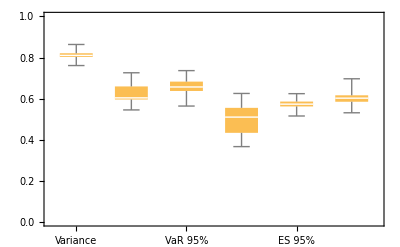

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

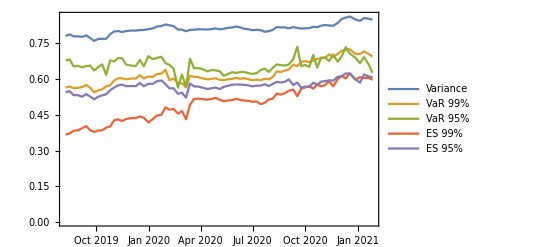

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

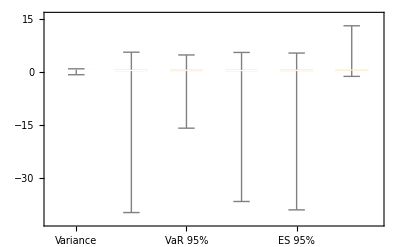

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

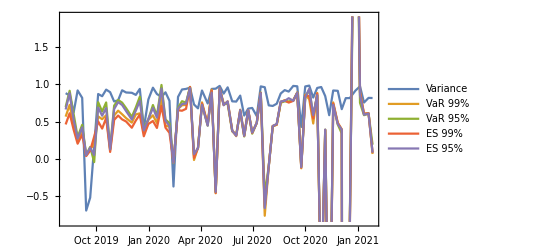

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

### In-sample P&L

```mathematica
For[kk=0, kk≤74, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{data⟦k,2⟧,{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,6⟧];
brr=Reverse[data⟦2;;All,5⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤74, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{data⟦k,2⟧,{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,6⟧];
brr=Reverse[data⟦2;;All,5⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤74, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{data⟦k,2⟧,{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,6⟧];
brr=Reverse[data⟦2;;All,5⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk≤74, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{data⟦k,2⟧,{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,6⟧];
brr=Reverse[data⟦2;;All,5⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤74, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

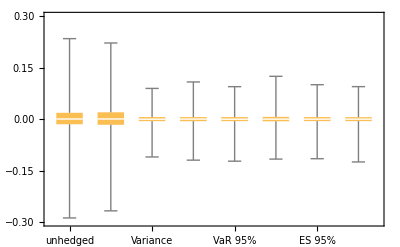

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

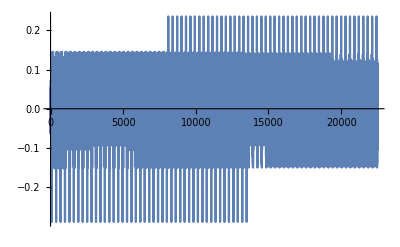

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤74, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

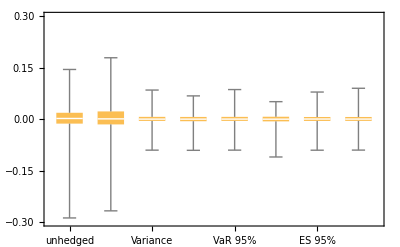

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

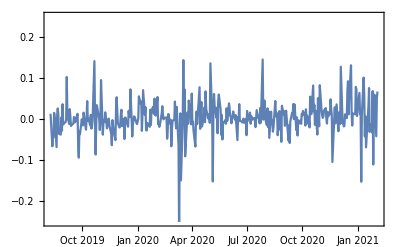
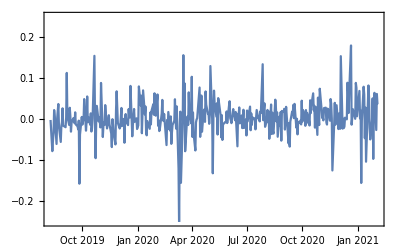

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

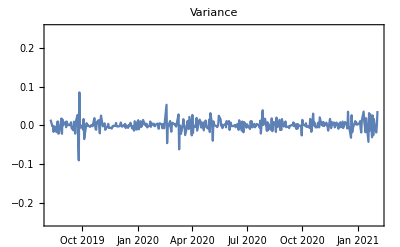
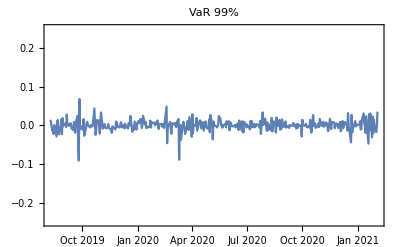
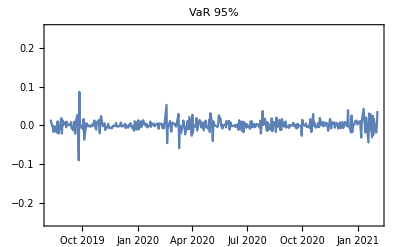
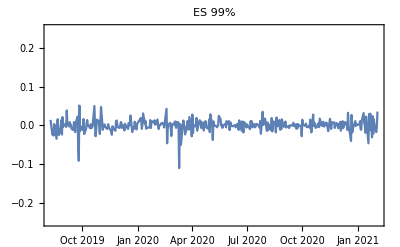
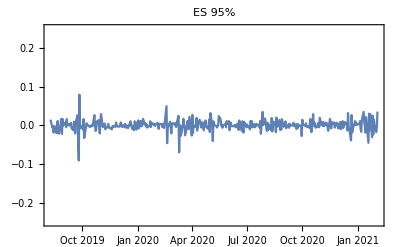
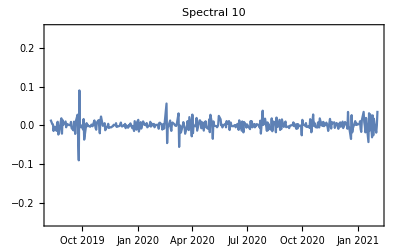

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤74, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

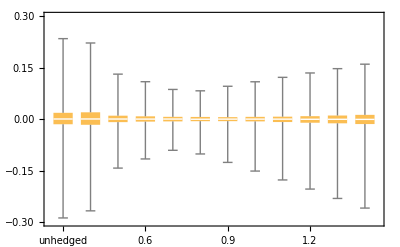

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤74, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

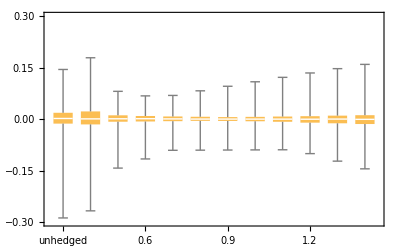

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤74, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-01-27 | 0.861697 | 0.90724 | 0.858251 | 0.90097 | 0.900107 | 0.845874
2021-01-20 | 0.858795 | 0.911378 | 0.872091 | 0.902477 | 0.87855 | 0.8555
2021-01-12 | 0.864889 | 0.917111 | 0.88249 | 0.906657 | 0.891102 | 0.871234
2021-01-05 | 0.854877 | 0.913529 | 0.76534 | 0.903447 | 0.867469 | 0.8658
2020-12-28 | 0.857776 | 0.913705 | 0.787804 | 0.902536 | 0.874686 | 0.872473
2020-12-18 | 0.87334 | 0.930919 | 0.804835 | 0.914826 | 0.906892 | 0.888932
2020-12-11 | 0.868997 | 0.925976 | 0.812892 | 0.91115 | 0.922375 | 0.877076
2020-12-04 | 0.865124 | 0.921301 | 0.791471 | 0.909374 | 0.908767 | 0.861755
2020-11-27 | 0.852697 | 0.913878 | 0.867317 | 0.904849 | 0.882367 | 0.845002
2020-11-19 | 0.849299 | 0.90704 | 0.869951 | 0.889571 | 0.867008 | 0.884744
2020-11-12 | 0.849971 | 0.913078 | 0.860374 | 0.902701 | 0.865418 | 0.876136
2020-11-05 | 0.85058 | 0.905246 | 0.865706 | 0.893152 | 0.86412 | 0.856505
2020-10-29 | 0.848182 | 0.904067 | 0.864617 | 0.890662 | 0.86353 | 0.884328
2020-10-22 | 0.845546 | 0.90239 | 0.868436 | 0.892626 | 0.869814 | 0.831041
2020-10-15 | 0.843691 | 0.899063 | 0.860168 | 0.88176 | 0.863882 | 0.877743
2020-10-08 | 0.842406 | 0.894889 | 0.859429 | 0.882811 | 0.855451 | 0.856438
2020-10-01 | 0.841612 | 0.896913 | 0.86403 | 0.883525 | 0.8577 | 0.82818
2020-09-24 | 0.840848 | 0.895922 | 0.859813 | 0.883102 | 0.874074 | 0.833981
2020-09-17 | 0.844579 | 0.885178 | 0.891271 | 0.865494 | 0.857726 | 0.852007
2020-09-10 | 0.850481 | 0.888836 | 0.877198 | 0.875857 | 0.878191 | 0.848304
2020-09-02 | 0.840246 | 0.876125 | 0.882629 | 0.866487 | 0.934327 | 0.840598
2020-08-26 | 0.824932 | 0.87355 | 0.82391 | 0.861045 | 0.845409 | 0.868543
2020-08-19 | 0.822652 | 0.870228 | 0.824558 | 0.857678 | 0.844088 | 0.820169
2020-08-12 | 0.822185 | 0.871797 | 0.826383 | 0.860947 | 0.842921 | 0.853373
2020-08-05 | 0.820589 | 0.858025 | 0.830879 | 0.847639 | 0.851604 | 0.822155
2020-07-29 | 0.81824 | 0.853119 | 0.816692 | 0.843876 | 0.856601 | 0.831521
2020-07-22 | 0.814721 | 0.854317 | 0.828292 | 0.843508 | 0.844749 | 0.82222
2020-07-15 | 0.827084 | 0.852875 | 0.82474 | 0.837347 | 0.845228 | 0.846115
2020-07-08 | 0.829067 | 0.853094 | 0.819165 | 0.843055 | 0.848795 | 0.84001
2020-06-30 | 0.826314 | 0.862666 | 0.815123 | 0.837724 | 0.851489 | 0.836331
2020-06-23 | 0.82877 | 0.853423 | 0.821308 | 0.841384 | 0.84998 | 0.835112
2020-06-16 | 0.828245 | 0.85574 | 0.823728 | 0.842806 | 0.848206 | 0.834655
2020-06-09 | 0.834062 | 0.854317 | 0.819879 | 0.842253 | 0.847153 | 0.837461
2020-06-02 | 0.835757 | 0.861201 | 0.819356 | 0.844115 | 0.850387 | 0.845986
2020-05-26 | 0.83398 | 0.854163 | 0.820762 | 0.841062 | 0.847153 | 0.837845
2020-05-18 | 0.833287 | 0.853261 | 0.810048 | 0.841342 | 0.8518 | 0.867202
2020-05-11 | 0.829956 | 0.851042 | 0.806006 | 0.83901 | 0.853 | 0.838499
2020-05-04 | 0.823955 | 0.853333 | 0.819185 | 0.841515 | 0.818771 | 0.862866
2020-04-27 | 0.822995 | 0.857032 | 0.823769 | 0.846807 | 0.822326 | 0.853781
2020-04-20 | 0.820754 | 0.856948 | 0.825054 | 0.843975 | 0.819676 | 0.848764
2020-04-13 | 0.821398 | 0.85439 | 0.818352 | 0.842777 | 0.818481 | 0.849924
2020-04-03 | 0.821491 | 0.863412 | 0.832842 | 0.844942 | 0.827655 | 0.846761
2020-03-27 | 0.825828 | 0.859913 | 0.834751 | 0.847845 | 0.829055 | 0.847829
2020-03-20 | 0.824868 | 0.860413 | 0.834896 | 0.848702 | 0.827301 | 0.866636
2020-03-13 | 0.822037 | 0.86279 | 0.843413 | 0.842939 | 0.815445 | 0.867822
2020-03-06 | 0.811195 | 0.704645 | 0.823581 | 0.621813 | 0.780104 | 0.836097
2020-02-28 | 0.816288 | 0.753143 | 0.809962 | 0.67609 | 0.768865 | 0.88236
2020-02-21 | 0.814043 | 0.725311 | 0.817544 | 0.62803 | 0.743435 | 0.851586
2020-02-13 | 0.821999 | 0.740424 | 0.818965 | 0.641684 | 0.756265 | 0.876074
2020-02-06 | 0.821332 | 0.733882 | 0.81587 | 0.593586 | 0.753381 | 0.891839
2020-01-30 | 0.821653 | 0.688618 | 0.816223 | 0.647105 | 0.791251 | 0.875859
2020-01-23 | 0.817346 | 0.679859 | 0.818938 | 0.587119 | 0.779738 | 0.865258
2020-01-15 | 0.816373 | 0.677122 | 0.816259 | 0.584602 | 0.778229 | 0.86489
2020-01-08 | 0.811856 | 0.662963 | 0.820164 | 0.576881 | 0.776586 | 0.864685
2019-12-31 | 0.812149 | 0.630884 | 0.816266 | 0.563908 | 0.781206 | 0.880043
2019-12-23 | 0.811273 | 0.707861 | 0.82022 | 0.609007 | 0.766925 | 0.845084
2019-12-16 | 0.811195 | 0.603236 | 0.824025 | 0.586317 | 0.767106 | 0.831247
2019-12-09 | 0.810073 | 0.707307 | 0.818201 | 0.61013 | 0.767387 | 0.835988
2019-12-02 | 0.810592 | 0.707933 | 0.819998 | 0.608718 | 0.768485 | 0.836737
2019-11-22 | 0.810436 | 0.656938 | 0.817182 | 0.602307 | 0.769755 | 0.837863
2019-11-15 | 0.808218 | 0.641451 | 0.808933 | 0.567836 | 0.775327 | 0.875486
2019-11-08 | 0.812159 | 0.650852 | 0.816485 | 0.584812 | 0.766364 | 0.832547
2019-11-01 | 0.810591 | 0.668919 | 0.820405 | 0.600625 | 0.767235 | 0.840272
2019-10-25 | 0.807289 | 0.717291 | 0.819772 | 0.555905 | 0.764634 | 0.833162
2019-10-18 | 0.798381 | 0.643704 | 0.833641 | 0.603867 | 0.751055 | 0.833717
2019-10-11 | 0.803767 | 0.693326 | 0.826963 | 0.529114 | 0.754048 | 0.836589
2019-10-04 | 0.804308 | 0.623393 | 0.831696 | 0.549276 | 0.75497 | 0.82978
2019-09-27 | 0.803612 | 0.640053 | 0.832699 | 0.548825 | 0.753678 | 0.830403
2019-09-20 | 0.81678 | 0.690169 | 0.827488 | 0.566893 | 0.773281 | 0.855722
2019-09-13 | 0.823324 | 0.680435 | 0.816096 | 0.583995 | 0.773281 | 0.860017
2019-09-06 | 0.819143 | 0.725158 | 0.830354 | 0.591004 | 0.768244 | 0.855422
2019-08-29 | 0.825167 | 0.668269 | 0.829651 | 0.578349 | 0.771902 | 0.874596
2019-08-22 | 0.825094 | 0.68377 | 0.885605 | 0.577836 | 0.772734 | 0.864916
2019-08-15 | 0.82891 | 0.640981 | 0.819281 | 0.54138 | 0.780141 | 0.882039
2019-08-08 | 0.825166 | 0.66628 | 0.817855 | 0.543133 | 0.779037 | 0.89456)

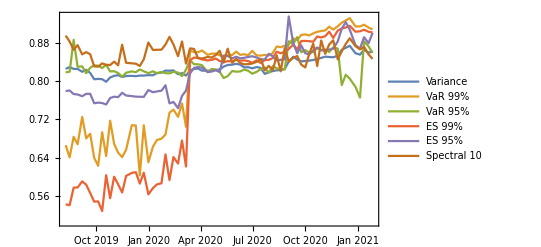

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods]
```